# Minimax Approximation Polynomials for Ndfloat16 Protocols

## 1. Inversion

```mathematica
ClearAll[MaxErrInv, SymmetricReciprocalPolynomial, SymmetricReciprocalNewton];

MaxErrInv[approx_,{x_,a_,b_}]:=NMaxValue[{Abs[approx-1/x],a<=x<=b},x, WorkingPrecision->40]

SymmetricReciprocalPolynomial[x_,degree_Integer?NonNegative]:=
Module[{t,residual,q},
residual=ChebyshevT[degree+1,(8 t-5)/3]/ChebyshevT[degree+1,-5/3];
q=Cancel[(1-residual)/t];
Expand[x q/. t->x^2]
]

SymmetricReciprocalNewton[x_,seedDegree_Integer?NonNegative,newtonSteps_Integer?NonNegative]:=Module[{seed},seed=SymmetricReciprocalPolynomial[x,seedDegree];
Nest[Expand[# (2-x #)]&,seed,newtonSteps]]
```

```mathematica
SymmetricReciprocalNewton[x, 2, 1]
```

(4368 x)/365-(7573056 x^3)/133225+(3653632 x^5)/26645-(23691264 x^7)/133225+(3145728 x^9)/26645-(4194304 x^11)/133225

```mathematica
(4368 x)/365-(7573056 x^3)/133225+(3653632 x^5)/26645-(23691264 x^7)/133225+(3145728 x^9)/26645-(4194304 x^11)/133225
```

(4368 x)/365-(7573056 x^3)/133225+(3653632 x^5)/26645-(23691264 x^7)/133225+(3145728 x^9)/26645-(4194304 x^11)/133225

```mathematica
MaxErrInv[SymmetricReciprocalNewton[x, 2, 1], {x, 1/2, 1}]
```

0.01094389191217864514918371176580972039782

```mathematica
data = Flatten[
Table[
{i, j, MaxErrInv[SymmetricReciprocalNewton[x, i, j], {x, 1/2, 1}]},
{i, 0,3}, 
{j, 0, 3}], 1];
TableForm[data,TableHeadings->{None,{"i","j","maxError"}}]
```

i | j | maxError
0 | 0 | 1.2
0 | 1 | 0.72
0 | 2 | 0.2592
0 | 3 | 0.03359232
1 | 0 | 0.4390243902439024390243902439024390243902
1 | 1 | 0.09637120761451516954193932183224271267103
1 | 2 | 0.004643704828539993297380776364313896327396
1 | 3 | 0.00001078199726730282427428054733796080907198
2 | 0 | 0.1479452054794520547945205479452054794521
2 | 1 | 0.01094389191217864514918371176580972039782
2 | 2 | 0.00005988438509272458107528561364064767250901
2 | 3 | 1.356731666925219940279022078458922561296×10^-9
3 | 0 | 0.04937519049070405364218226150563852483999
3 | 1 | 0.001218954717996656002748175306905431427016
3 | 2 | 7.429253022631535807729148474022837233364×10^-7
3 | 3 | 2.759690023713990555027240599634290600771×10^-13

Based on the table, choose `SymmetricReciprocalPolynomial[x, 1]` and 2 iterations of Newton’s method.

```mathematica
SymmetricReciprocalPolynomial[x, 1]
```

(160 x)/41-(128 x^3)/41

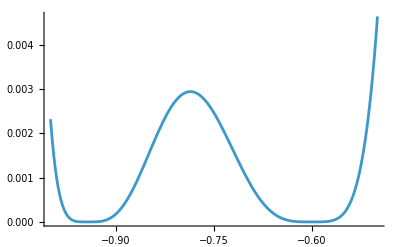

```mathematica
Plot[Abs[SymmetricReciprocalNewton[x, 1, 2] - (1/x)], {x, -1, -0.5}]
```

## 2. Square Root

```mathematica
ClearAll[SqrtChebyshevPolynomial, SqrtChebyshevRationalPolynomial, MaxErrSqrt]

SqrtChebyshevPolynomial[
   x_,
   degree_Integer?NonNegative,
   precision_: 50
] :=
 Module[{nodes, values},

   nodes = N[
     Table[
       3/4 + 1/4 Cos[(2 k + 1) Pi/(2 degree + 2)],
       {k, 0, degree}
     ],
     precision
   ];

   values = Sqrt[nodes];

   Expand[
     InterpolatingPolynomial[
       Transpose[{nodes, values}],
       x
     ]]]

SqrtChebyshevRationalPolynomial[x_,degree_Integer?NonNegative,tolerance_:2^-14]:=Rationalize[SqrtChebyshevPolynomial[x,degree,80],tolerance]
MaxErrSqrt[approx_,{x_,a_,b_}]:=NMaxValue[{Abs[approx-Sqrt[x]],a<=x<=b},x, WorkingPrecision->40]
```

```mathematica
data = Table[
{i, MaxErrSqrt[SqrtChebyshevPolynomial[x, i], {x, 1/2, 1}]},
{i, 0,4}];
TableForm[data,TableHeadings->{None,{"i","maxError"}}]
```

i | maxError
0 | 0.1589186225978911223628788086480871441866
1 | 0.007431885767291104998503856105482144287015
2 | 0.000664027538893010189135587688800747174456
3 | 0.0000729541630225738729449632109157602004622
4 | 8.904863373085309109491032585078110039196×10^-6

```mathematica
SqrtChebyshevRationalPolynomial[x, 2]
```

13/41+(191 x)/217-(17 x^2)/86

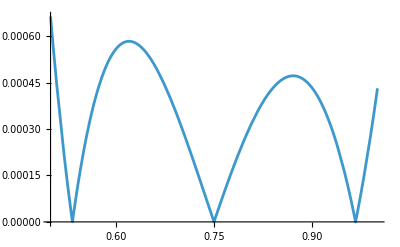

```mathematica
Plot[{Abs[SqrtChebyshevPolynomial[x, 2] - Sqrt[x]]}, {x, 1/2, 1}]
```

## 3. Logarithm

```mathematica
ClearAll[Log2ChebyshevPolynomial,Log2ChebyshevRationalPolynomial ,MaxErrLog2];

Log2ChebyshevPolynomial[x_,degree_Integer?NonNegative,precision_:50]:=Module[{nodes,values},nodes=N[Table[3/4+1/4 Cos[(2 k+1) Pi/(2 degree+2)],{k,0,degree}],precision];
values=Log[2,nodes];
Expand[InterpolatingPolynomial[Transpose[{nodes,values}],x]]]

Log2ChebyshevRationalPolynomial[x_,degree_Integer?NonNegative,tolerance_:2^-16]:=Rationalize[Log2ChebyshevPolynomial[x,degree,80],tolerance]

MaxErrLog2[approx_,{x_,a_,b_}]:=NMaxValue[{Abs[approx-Log2[x]],a<=x<=b},x, WorkingPrecision->40]
```

```mathematica
data = Table[
{i, MaxErrLog2[Log2ChebyshevPolynomial[x, i], {x, 1/2, 1}]},
{i, 0,4}];
TableForm[data,TableHeadings->{None,{"i","maxError"}}]
```

i | maxError
0 | 0.5849625007211561814537389439478165087598
1 | 0.05361838480937757651564409371515432473012
2 | 0.006308174563858836239494272919974729274612
3 | 0.000825462822934166279027627807108118554038
4 | 0.0001145799603822780741549077301545441766922

```mathematica
Log2ChebyshevRationalPolynomial[x, 2]
```

-719/271+(343 x)/86-(79 x^2)/59

## 4. Exponent

```mathematica
ClearAll[Pow2ChebyshevPolynomial,Pow2ChebyshevRationalPolynomial,MaxErrPow2]

Pow2ChebyshevPolynomial[r_,degree_Integer?NonNegative,precision_:50]:=Module[{nodes,values},nodes=N[Table[1/2 Cos[(2 k+1) Pi/(2 degree+2)],{k,0,degree}],precision];
values=2^nodes;
Expand[InterpolatingPolynomial[Transpose[{nodes,values}],r]]]

Pow2ChebyshevRationalPolynomial[x_,degree_Integer?NonNegative,tolerance_:2^-16]:=Rationalize[Pow2ChebyshevPolynomial[x,degree,80],tolerance]

MaxErrPow2[approx_,{x_,a_,b_}]:=NMaxValue[{Abs[approx-(2^x)],a<=x<=b},x, WorkingPrecision->40]
```

```mathematica
data = Table[
{i, MaxErrPow2[Pow2ChebyshevPolynomial[x, i], {x, 1/2, 1}]},
{i, 0,4}];
TableForm[data,TableHeadings->{None,{"i","maxError"}}]
```

i | maxError
0 | 1.
1 | 0.2697150445467336758660999313868262423944
2 | 0.054363492415677750367048869672769109722
3 | 0.008460947673029378348894372082420355474446
4 | 0.001067120058727984058838921284511941627988

```mathematica
Pow2ChebyshevRationalPolynomial[x, 3]
```

11025/11026+(131 x)/189+(33 x^2)/136+(11 x^3)/197